## Primer

### 1.1.1 Paths in Euclidean space

Figure 1

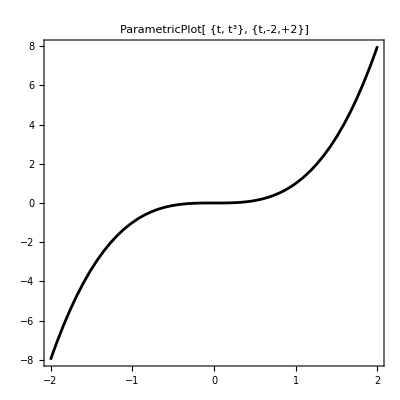

```mathematica
ParametricPlot[{t,t^3},{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {t, t^3}, {t,-2,+2}]"],16]]
```

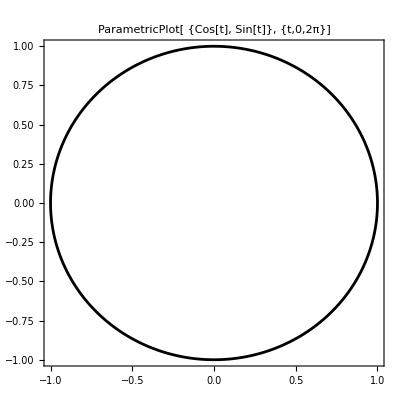

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ {Cos[t], Sin[t]}, {t,0,2π}]"],16]]
```

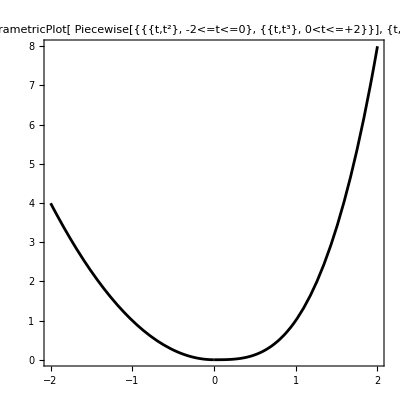

```mathematica
ParametricPlot[Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,t^2}, -2<=t<=0}, {{t,t^3}, 0<t<=+2}}], {t,-2,+2}]"],16]]
```

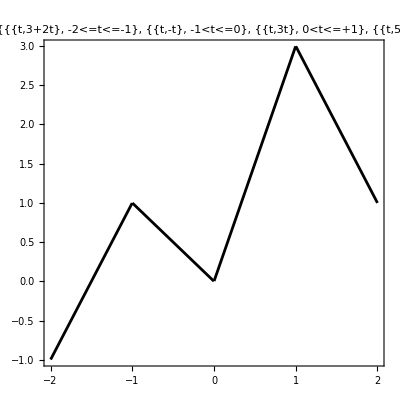

```mathematica
ParametricPlot[Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}],{t,-2,2},Frame->True,AspectRatio->1,
AxesStyle->{{Dashed,Gray},{Dashed,Gray}},PlotStyle->Black,
PlotLabel->Style[Framed["ParametricPlot[ Piecewise[{{{t,3+2t}, -2<=t<=-1}, {{t,-t}, -1<t<=0}, {{t,3t}, 0<t<=+1}, {{t,5-2t}, +1<t<=+2}}], {t,-2,+2}]"],16]]
```

### 1.1.2 Path integrals

The scalar line integral of the function f along a curve C={r(u)∈ℝ^n,a≤u≤b} is given by:

-Graphics-"∮_C f(x)ⅆx=∫_a^b f(r(u)) Norm[r'(u)]ⅆu"

∫_a^b f(X_t) ⅆ X_t=∫_a^b f(X_t) ⅆt=∫_a^b f(X_t)dX_t/dt ⅆt

```mathematica
LineIntegrate[t^2,{x}∈ParametricRegion[{t^3},{{t,0,1}}]]
```

3/5

```mathematica
nrsign[d_,k_]:=If[d==1,k+1,(d^(k+1)-1)/(d-1)];
```

```mathematica
Table[nrsign[2,k]-1,{k,1,12}]
```

{2,6,14,30,62,126,254,510,1022,2046,4094,8190}

### 1.2.2 Examples

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[dim,Log[dim,Length[list]]]],list];
```

```mathematica
Map[tensorfold,{{1},{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}}]
```

{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}}

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
];
```

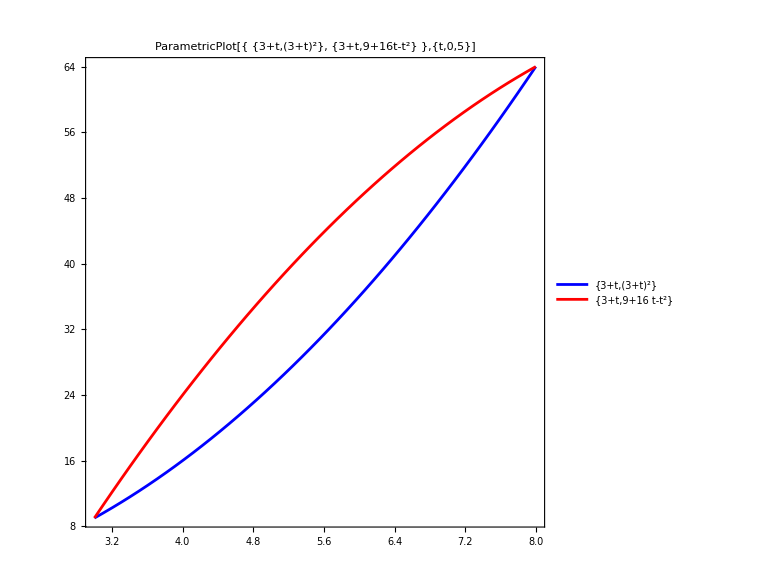

```mathematica
ParametricPlot[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{t,0,5},
Frame->True,AspectRatio->1,PlotLegends->"Expressions",
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
AxesOrigin->{3,9},PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"ParametricPlot[{
{3+t,(3+t)^2},
{3+t,9+16t-t^2}
},{t,0,5}]"],16]]
```

```mathematica
signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}]
```

{{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}},{{1},{5,55},{{25/2,350/3},{475/3,3025/2}},{{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}}}

### Sin

#### Plot and Signatures

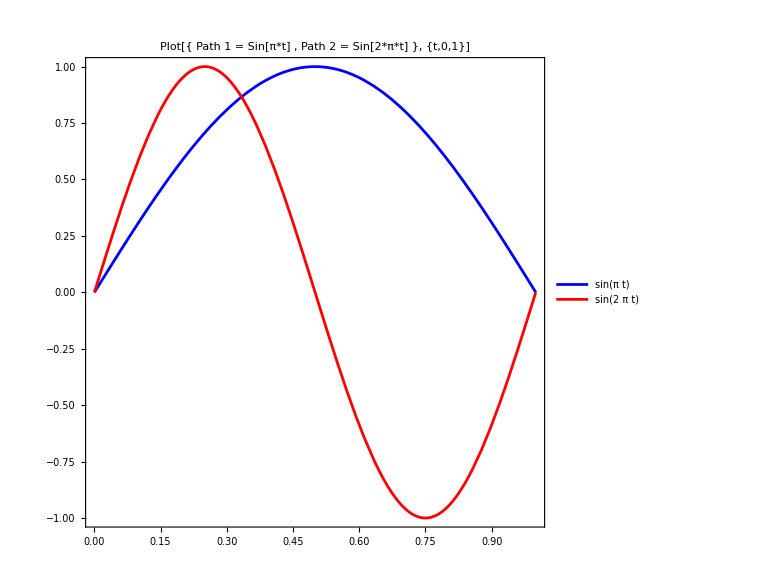

```mathematica
Plot[{Sin[π t],Sin[2π t]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 1 = Sin[π*t] ,
Path 2 = Sin[2*π*t] 
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins=signat[{{t,Sin[π t]},{t,Sin[2π t]}},{0,1},5]]
```

{135.83,{{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}},{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}}}

```mathematica
{sigsins1f,sigsins2f}=sigsins;
```

```mathematica
sigsins1f
```

{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins1f[[5]]
```

{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}

```mathematica
sigsins2f
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}

```mathematica
sigsins2f[[5]]
```

{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}

```mathematica
N[sigsins1f]
```

{{1.},{1.,0.},{{0.5,-0.63662},{0.63662,0.}},{{{0.166667,-0.31831},{0.,0.25}},{{0.31831,-0.5},{0.25,0.}}},{{{{0.0416667,-0.0946519},{-0.0343543,0.125}},{{0.0343543,-0.0473576},{0.0473576,-0.0707355}}},{{{0.0946519,-0.202642},{-0.0473576,0.212207}},{{0.125,-0.212207},{0.0707355,0.}}}},{{{{{0.00833333,-0.0208001},{-0.0114514,0.0353341}},{{0.,0.0053227},{0.013675,-0.0353678}}},{{{0.0114514,-0.0253303},{-0.00734245,0.0265258}},{{0.013675,-0.0265258},{0.,0.015625}}}},{{{{0.0208001,-0.0506606},{-0.0253303,0.0795775}},{{0.0053227,0.},{0.0265258,-0.0625}}},{{{0.0353341,-0.0795775},{-0.0265258,0.09375}},{{0.0353678,-0.0625},{0.015625,0.}}}}}}

```mathematica
N[sigsins1f[[5]]]
```

{{{{0.0416667,-0.0946519},{-0.0343543,0.125}},{{0.0343543,-0.0473576},{0.0473576,-0.0707355}}},{{{0.0946519,-0.202642},{-0.0473576,0.212207}},{{0.125,-0.212207},{0.0707355,0.}}}}

```mathematica
N[sigsins2f]
```

{{1.},{1.,0.},{{0.5,0.},{0.,0.}},{{{0.166667,0.159155},{-0.31831,0.25}},{{0.159155,-0.5},{0.25,0.}}},{{{{0.0416667,0.0795775},{-0.0795775,0.125}},{{-0.0795775,-0.25},{0.25,0.}}},{{{0.0795775,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}},{{{{{0.00833333,0.0224944},{-0.0104001,0.0400835}},{{-0.0241887,-0.0611693},{0.0659188,0.0176839}}},{{{-0.0104001,-0.0569932},{-0.013675,-0.0928404}},{{0.0659188,0.172418},{-0.114945,0.015625}}}},{{{{0.0224944,0.0379954},{-0.0569932,0.0397887}},{{-0.0611693,-0.159155},{0.172418,-0.0625}}},{{{0.0400835,0.0397887},{-0.0928404,0.09375}},{{0.0176839,-0.0625},{0.015625,0.}}}}}}

```mathematica
N[sigsins2f[[5]]]
```

{{{{0.0416667,0.0795775},{-0.0795775,0.125}},{{-0.0795775,-0.25},{0.25,0.}}},{{{0.0795775,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}}

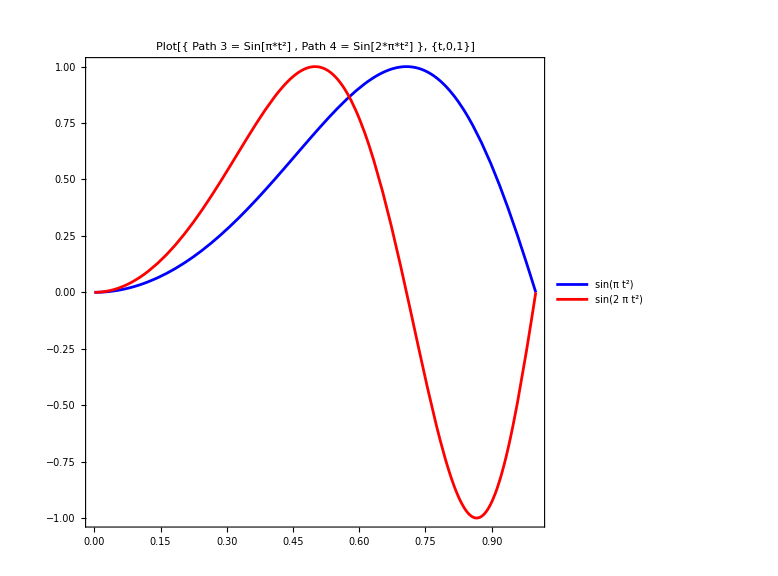

```mathematica
Plot[{Sin[π t^2],Sin[2π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 3 = Sin[π*t^2] ,
Path 4 = Sin[2*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins2=signat[{{t,Sin[π t^2]},{t,Sin[2π t^2]}},{0,1},4]]
```

{42.2397,{{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}}},{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}}}}}

```mathematica
{sigsins1f2,sigsins2f2}=sigsins2;
```

```mathematica
sigsins1f2
```

{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}}}

```mathematica
sigsins2f2
```

{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}}}

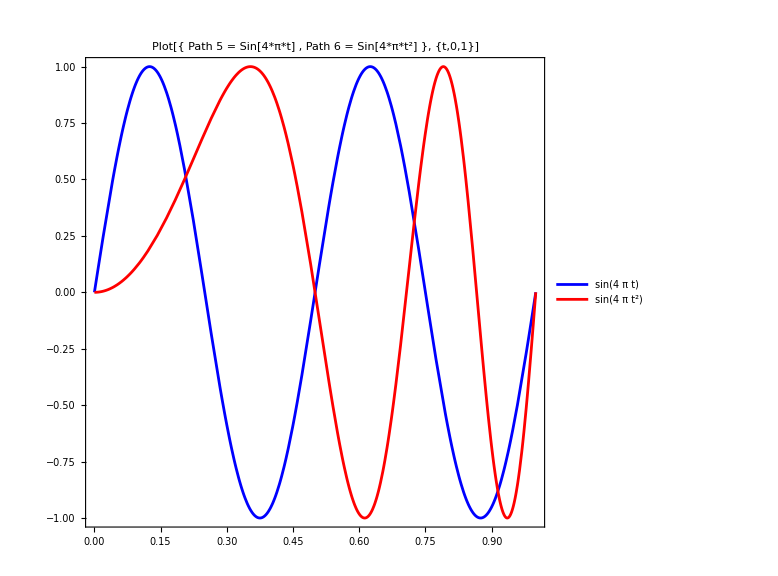

```mathematica
Plot[{Sin[4π t],Sin[4π t^2]},{t,0,1},Frame->True,
PlotRange->All,PlotLegends->"Expressions",AspectRatio->1,
ImageSize->Large,AxesStyle->{{Dashed,Gray},{Dashed,Gray}},
PlotStyle->{Blue,Red},
PlotLabel->Style[Framed[
"Plot[{
Path 5 = Sin[4*π*t] ,
Path 6 = Sin[4*π*t^2]
}, {t,0,1}]"],16]]
```

```mathematica
Timing[sigsins42=signat[{{t,Sin[4π t]},{t,Sin[4π t^2]}},{0,1},4]]
```

{46.8146,{{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}},{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}}}

```mathematica
{sigsins1f42,sigsins2f42}=sigsins42;
```

```mathematica
sigsins1f42
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}},{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}}

```mathematica
sigsins2f42
```

{{1},{1,0},{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}},{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/16 (4-FresnelC[4])}},{{FresnelS[2 √2]/(2 √2),1/8 (-4+FresnelC[4])},{1/16 (4-FresnelC[4]),0}}},{{{{1/24,(4-√2 FresnelC[2 √2])/(64 π)},{(3 (-4+√2 FresnelC[2 √2]))/(64 π),1/8}},{{(12-3 √2 FresnelC[2 √2]-8 √2 π FresnelS[2 √2])/(64 π),1/16 (-4+FresnelS[2 √2]^2)},{1/16 (4-FresnelC[4]-FresnelS[2 √2]^2),1/288 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])}}},{{{(-4+√2 FresnelC[2 √2]+8 √2 π FresnelS[2 √2])/(64 π),-1/16 FresnelS[2 √2]^2},{1/16 (-4+2 FresnelC[4]+FresnelS[2 √2]^2),1/96 (9 √2 FresnelS[2 √2]-√6 FresnelS[2 √6])}},{{1/16 (2-FresnelC[4]),1/96 (-9 √2 FresnelS[2 √2]+√6 FresnelS[2 √6])},{(3 √3 FresnelS[2 √2]-FresnelS[2 √6])/(48 √6),0}}}}}

```mathematica
N[sigsins1f42]
```

{{1.},{1.,0.},{{0.5,0.},{0.,0.}},{{{0.166667,0.0795775},{-0.159155,0.25}},{{0.0795775,-0.5},{0.25,0.}}},{{{{0.0416667,0.0397887},{-0.0397887,0.125}},{{-0.0397887,-0.25},{0.25,0.}}},{{{0.0397887,0.},{-0.25,0.}},{{0.125,0.},{0.,0.}}}}}

```mathematica
N[sigsins2f42]
```

{{1.},{1.,0.},{{0.5,-0.137168},{0.137168,0.}},{{{0.166667,0.},{-0.137168,0.218848}},{{0.137168,-0.437697},{0.218848,0.}}},{{{{0.0416667,0.0164083},{-0.049225,0.125}},{{-0.0193589,-0.240593},{0.209441,-0.0134457}}},{{{0.0521756,-0.0094075},{-0.178289,0.0403371}},{{0.0938484,-0.0403371},{0.0134457,0.}}}}}

```mathematica
Grid[{{sigsins1f[[2]]},{sigsins2f[[2]]},{sigsins1f2[[2]]},{sigsins2f2[[2]]},{sigsins1f42[[2]]},{sigsins2f42[[2]]}}]
```

{1,0}
{1,0}
{1,0}
{1,0}
{1,0}
{1,0}

```mathematica
Grid[{{sigsins1f[[3]]},{sigsins2f[[3]]},{sigsins1f2[[3]]},{sigsins2f2[[3]]},{sigsins1f42[[3]]},{sigsins2f42[[3]]}},Frame->All]
```

{{1/2,-2/π},{2/π,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}}
{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}}
{{1/2,0},{0,0}}
{{1/2,-FresnelS[2 √2]/(2 √2)},{FresnelS[2 √2]/(2 √2),0}}

```mathematica
Grid[Expand[{{sigsins1f[[4]]},{sigsins2f[[4]]},{sigsins1f2[[4]]},{sigsins2f2[[4]]},{sigsins1f42[[4]]},{sigsins2f42[[4]]}}],Frame->All]
```

{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}}
{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}}
{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/4-FresnelC[2]/8}},{{-1/π+FresnelS[√2]/(√2),-1/2+FresnelC[2]/4},{1/4-FresnelC[2]/8,0}}}
{{{1/6,0},{-FresnelS[2]/2,1/4-FresnelC[2 √2]/(8 √2)}},{{FresnelS[2]/2,-1/2+FresnelC[2 √2]/(4 √2)},{1/4-FresnelC[2 √2]/(8 √2),0}}}
{{{1/6,1/(4 π)},{-1/(2 π),1/4}},{{1/(4 π),-1/2},{1/4,0}}}
{{{1/6,0},{-FresnelS[2 √2]/(2 √2),1/4-FresnelC[4]/16}},{{FresnelS[2 √2]/(2 √2),-1/2+FresnelC[4]/8},{1/4-FresnelC[4]/16,0}}}

```mathematica
Grid[Expand[{{sigsins1f[[5]]},{sigsins2f[[5]]},{sigsins1f2[[5]]},{sigsins2f2[[5]]},{sigsins1f42[[5]]},{sigsins2f42[[5]]}}],Frame->All]
```

{{{{1/24,2/π^3-1/(2 π)},{-6/π^3+1/(2 π),1/8}},{{6/π^3-1/(2 π),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{-2/π^3+1/(2 π),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}}
{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,-1/(4 π)-FresnelC[√2]/(4 √2 π)},{-1/(4 π)+(3 FresnelC[√2])/(4 √2 π),1/8}},{{5/(4 π)-(3 FresnelC[√2])/(4 √2 π)-FresnelS[√2]/(2 √2),-1/4+1/4 FresnelS[√2]^2},{1/4-FresnelC[2]/8-1/4 FresnelS[√2]^2,-FresnelS[√2]/(8 √2)+FresnelS[√6]/(24 √6)}}},{{{-3/(4 π)+FresnelC[√2]/(4 √2 π)+FresnelS[√2]/(2 √2),-1/4 FresnelS[√2]^2},{-1/4+FresnelC[2]/4+1/4 FresnelS[√2]^2,(3 FresnelS[√2])/(8 √2)-FresnelS[√6]/(8 √6)}},{{1/8-FresnelC[2]/8,-(3 FresnelS[√2])/(8 √2)+FresnelS[√6]/(8 √6)},{FresnelS[√2]/(8 √2)-FresnelS[√6]/(24 √6),0}}}}
{{{{1/24,1/(8 π)-FresnelC[2]/(16 π)},{-3/(8 π)+(3 FresnelC[2])/(16 π),1/8}},{{3/(8 π)-(3 FresnelC[2])/(16 π)-FresnelS[2]/4,-1/4+FresnelS[2]^2/8},{1/4-FresnelC[2 √2]/(8 √2)-FresnelS[2]^2/8,-FresnelS[2]/16+FresnelS[2 √3]/(48 √3)}}},{{{-1/(8 π)+FresnelC[2]/(16 π)+FresnelS[2]/4,-1/8 FresnelS[2]^2},{-1/4+FresnelC[2 √2]/(4 √2)+FresnelS[2]^2/8,(3 FresnelS[2])/16-FresnelS[2 √3]/(16 √3)}},{{1/8-FresnelC[2 √2]/(8 √2),-(3 FresnelS[2])/16+FresnelS[2 √3]/(16 √3)},{FresnelS[2]/16-FresnelS[2 √3]/(48 √3),0}}}}
{{{{1/24,1/(8 π)},{-1/(8 π),1/8}},{{-1/(8 π),-1/4},{1/4,0}}},{{{1/(8 π),0},{-1/4,0}},{{1/8,0},{0,0}}}}
{{{{1/24,1/(16 π)-FresnelC[2 √2]/(32 √2 π)},{-3/(16 π)+(3 FresnelC[2 √2])/(32 √2 π),1/8}},{{3/(16 π)-(3 FresnelC[2 √2])/(32 √2 π)-FresnelS[2 √2]/(4 √2),-1/4+1/16 FresnelS[2 √2]^2},{1/4-FresnelC[4]/16-1/16 FresnelS[2 √2]^2,-FresnelS[2 √2]/(16 √2)+FresnelS[2 √6]/(48 √6)}}},{{{-1/(16 π)+FresnelC[2 √2]/(32 √2 π)+FresnelS[2 √2]/(4 √2),-1/16 FresnelS[2 √2]^2},{-1/4+FresnelC[4]/8+1/16 FresnelS[2 √2]^2,(3 FresnelS[2 √2])/(16 √2)-FresnelS[2 √6]/(16 √6)}},{{1/8-FresnelC[4]/16,-(3 FresnelS[2 √2])/(16 √2)+FresnelS[2 √6]/(16 √6)},{FresnelS[2 √2]/(16 √2)-FresnelS[2 √6]/(48 √6),0}}}}

```mathematica
Timing[sigline=signat[{{Subscript[a, 1]+Subscript[b, 1]*t,Subscript[a, 2]+Subscript[b, 2]*t}},{0,T},2]]
```

{0.001902,{{{1},{T b_1,T b_2},{{1/2 T^2 b_1^2,1/2 T^2 b_1 b_2},{1/2 T^2 b_1 b_2,1/2 T^2 b_2^2}}}}}